```mathematica
f[x_]=√3*Exp[-1/22*x^3 +1/2*x-1/4]
```

√3 ⅇ^(-1/4+x/2-x^3/22)

```mathematica
a=0;b=6;n=10;x0=2.4316;h=(b-a)/n;
```

```mathematica
(*Возьмём таблицу значений функции для равноотстоящих узлов на промежутке для n=10:*)
```

```mathematica
data=Table[{i h,f[i h]},{i,0,n}]//N;
```

```mathematica
TableForm[data]
```

0. | 1.34892
0.6 | 1.80306
1.2 | 2.27223
1.8 | 2.54522
2.4 | 2.38916
3. | 1.77187
3.6 | 0.978807
4.2 | 0.379717
4.8 | 0.0975292
5.4 | 0.0156365
6. | 0.00147533

```mathematica
(*a


Степень многочлена,которым будет аппроксимирована функция:*)
m=1;
```

```mathematica
(*Коэффициенты каждой строки системы относительно Subscript[a, i]:*)
```

```mathematica
ACoeff1=Table[If[i+j!=0,∑_(k=0)^n (data[[k+1,1]])^(i+j),n+1], {i, 0, m}, {j, 0, m}]
```

{{11,33.},{33.,138.6}}

```mathematica
(*Столбец свободных членов:*)
```

```mathematica
B1:=Table[If[i!=0,∑_(k=0)^n (data[[k+1,2]]*(data[[k+1,1]])^i), ∑_(l=0)^n data[[l+1,2]]], {i, 0, m}];B1
```

{13.6036,25.1194}

```mathematica
(*Найдём значения Subscript[a, i]с помощью встроенной функции LinearSolve:*)
A1=LinearSolve[ACoeff1,B1]
```

{2.42544,-0.396248}

```mathematica
(*Тогда многочлен примет вид:*)
Q1[x_]=∑_(i=0)^m (A1[[i+1]]*x^i)
```

2.42544-0.396248 x

```mathematica
(*Изобразим полученный многочлен:*)
graphD=ListPlot[data,PlotStyle->{Darker,PointSize[0.02]}];
```

```mathematica
graphQ1=Plot[Q1[x],{x,a,b},PlotStyle->Yellow];
```

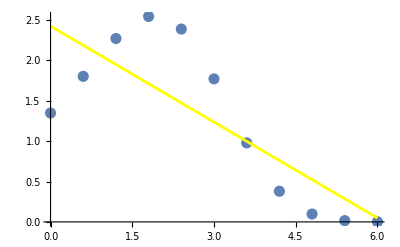

```mathematica
Show[graphD,graphQ1]
```

```mathematica
(*б

Аналогичным образом найдём многочлен второй степени.*)
m=2;
ACoeff2=Table[If[i+j!=0,∑_(k=0)^n (data[[k+1,1]])^(i+j),n+1], {i, 0, m}, {j, 0, m}]
```

{{11,33.,138.6},{33.,138.6,653.4},{138.6,653.4,3283.16}}

```mathematica
B2:=Table[If[i!=0,∑_(k=0)^n (data[[k+1,2]]*(data[[k+1,1]])^i), ∑_(l=0)^n data[[l+1,2]]], {i, 0, m}];B2
```

{13.6036,25.1194,64.0157}

```mathematica
A2=LinearSolve[ACoeff2,B2]
```

{1.7824,0.318234,-0.11908}

```mathematica
(*Многочлен примет вид:*)
```

```mathematica
Q2[x_]=∑_(i=0)^m (A2[[i+1]]*x^i)
```

1.7824+0.318234 x-0.11908 x^2

```mathematica
(*Изобразим полученный многочлен:*)
graphQ2=Plot[Q2[x],{x,a,b},PlotStyle->Orange];
```

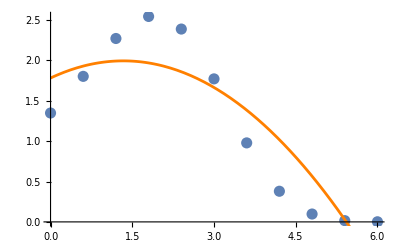

```mathematica
Show[graphD,graphQ2]
```

```mathematica
(*в

Построим многочлены наилучшего среднеквадратичного приближения третьей и четвертой степеней с помощью встроенной функции Fit:
*)
```

```mathematica
Q3[x_]=Fit[data,{1,x^1,x^2,x^3},x]
```

1.16915+1.94223 x-0.82887 x^2+0.0788655 x^3

```mathematica
Q4[x_]=Fit[data,{1,x^1,x^2,x^3,x^4},x]
```

1.2562+1.43842 x-0.409029 x^2-0.0330921 x^3+0.0093298 x^4

```mathematica
(*Изобразим полученные многочлены:*)
```

```mathematica
graphQ3=Plot[Q3[x],{x,a,b},PlotStyle->{Green,Thickness[0.01]}];
```

```mathematica
graphQ4=Plot[Q4[x],{x,a,b},PlotStyle->Red];
```

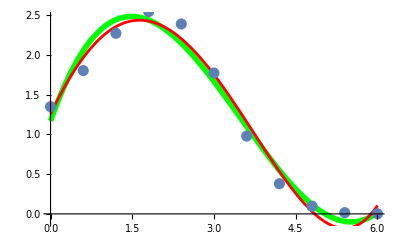

```mathematica
Show[graphQ3,graphQ4,graphD]
```

```mathematica
(*г
Значения полученных многочленов в точке x0:
*)
```

```mathematica
Print["Q1[x0]=",Q1[x0],", Q2[x0]=",Q2[x0],", Q3[x0]=",Q3[x0],", Q4[x0]=",Q4[x0]]
```

Q1[x0]=1.46192, Q2[x0]=1.85214, Q3[x0]=2.12491, Q4[x0]=2.18581

```mathematica
(*д
*)
```

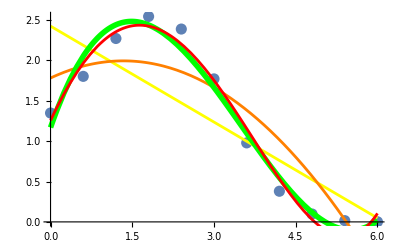

```mathematica
Show[graphD,graphQ1,graphQ2,graphQ3,graphQ4]
```

```mathematica
(*Как видно из графика,с увеличением степени многочлена аппроксимация методом наименьших квадратов даёт значения,всё более близкие к значениям исходной функции.*)
```